```mathematica
ClearAll
rau=0.2201
teta = 1.4161784471595336*(Pi/180)
alfa = 1.5 * Pi / 180
lambda =1.549802480415003*10^-08
k=2*Pi/lambda
h=2*k*Sin[teta]
chizero=-1.5057156520331863*10^-7+I*2.935993357131102*10^-11
chih = (-5.665963760105155-5.6630277667480283 * I )*10^-8
chimh=-I*chih
chih2=chih*chimh
u2=0.25*chih2*k^2
t = 1.0
p=20*10^3
rayon=2000
raygam = rayon * Cos[teta]
kp=k*Sin[2*teta]
kp2=kp*Sin[2*teta]
```

ClearAll

0.2201

0.024717

0.0261799

1.5498×10^-8

4.05418×10^8

2.00394×10^7

-1.50572×10^-7+2.93599×10^-11 ⅈ

-5.66596×10^-8-5.66303×10^-8 ⅈ

-5.66303×10^-8+5.66596×10^-8 ⅈ

6.4173×10^-15-3.32618×10^-18 ⅈ

263.694-0.136676 ⅈ

1.

20000

2000

1999.39

2.00333×10^7

989921.

```mathematica
sg=1
teta1=alfa+sg*teta
teta2=alfa-sg*teta
fam1=Sin[teta1]
fam2=Sin[teta2]
gam1=Cos[teta1]
gam2=Cos[teta2]
t1=t/gam1
t2=t/gam2
qpoly=p * rayon * gam2 / (2 * p + rayon * gam1)
att = Exp[-0.5*k*(t1+t2)* Im[chizero]];{"att",att}
s2max=0.25*t1*t2
u2max = u2 * s2max
gama=t2/t1
a=Sin[2*teta]*t1*0.5
kin=0.25*(t1-t2)*chizero/a
kinx=Re[kin]
kiny=Im[kin]
com=Sin[alfa]*(1+gam1*gam2*(1+rau))
kp3=0.5*k*(gama*a)^2
mu1=sg*(Cos[alfa]*2*fam1*gam1+Sin[alfa]*(fam1^2+rau*gam1^2))/(Sin[2*teta]*Cos[teta])
mu2=-sg * (Cos[alfa]*2*fam2*gam2+Sin[alfa]*(fam2^2+rau*gam2^2))/(Sin[2*teta]*Cos[teta])
a1=sg*(0.5*t/Cos[teta])*(Cos[alfa] * Sin[teta1]+ rau * Sin[alfa]Cos[teta1]) 
a2=-sg*(0.5*t/Cos[teta])*(Cos[alfa] * Sin[teta2]+ rau * Sin[alfa]Cos[teta2])
acrist=-sg*h*com/rayon
acmax=acrist * s2max
g=gama * acrist * rayon/kp2
kap=u2max/acmax
pe=p*rayon/(gama^2*(rayon+p*mu2)-g*p)
qe[q_]:=q*rayon/(rayon-q*mu1-g * q);
be[q_]:=1/qe[q]+1/pe;
invle[q_]:=1/(pe+qe[q])+ g / rayon;
sgplus[x_,q_]:=NIntegrate[Hypergeometric1F1[I*kap,1,I*acmax*(1-(v/a)^2)]*Exp[0.5*I*k * v^2 *invle[q]-k*v*kiny]*Cos[k*v*x/(q * pe * be[q])], {v,-a,a}];
```

1

0.0508969

0.00146296

0.0508749

0.00146296

0.998705

0.999999

1.0013

1.

952.439

{att,0.98816}

0.250324

66.0089-0.0342134 ⅈ

0.998706

0.0247389

-1.97136×10^-9+3.84395×10^-13 ⅈ

-1.97136×10^-9

3.84395×10^-13

0.058074

123740.

2.1741

-0.175845

0.0283144

-0.0036131

-581.884

-145.66

-1.1741

-0.453172+0.000234886 ⅈ

1820.75

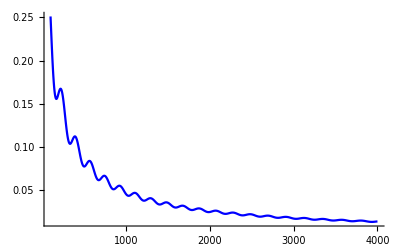

```mathematica
Plot[Abs[sgplus[0,q]^2*att/(lambda*q*p*be[q])],{q,100,4000},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{RGBColor[0,0,1]}]
```

```mathematica
sg=-1
teta1=alfa+sg*teta
teta2=alfa-sg*teta
fam1=Sin[teta1]
fam2=Sin[teta2]
gam1=Cos[teta1]
gam2=Cos[teta2]
t1=t/gam1
t2=t/gam2
qpoly=p * rayon * gam2 / (2 * p + rayon * gam1) ;
att = Exp[-0.5*k*(t1+t2)* Im[chizero]];{"att",att}
s2max=0.25*t1*t2
u2max = u2 * s2max
gama=t2/t1
a=Sin[2*teta]*t1*0.5
kin=0.25*(t1-t2)*chizero/a
kinx=Re[kin]
kiny=Im[kin]
com=Sin[alfa]*(1+gam1*gam2*(1+rau))
kp3=0.5*k*(gama*a)^2
mu1=sg*(Cos[alfa]*2*fam1*gam1+Sin[alfa]*(fam1^2+rau*gam1^2))/(Sin[2*teta]*Cos[teta])
mu2=-sg * (Cos[alfa]*2*fam2*gam2+Sin[alfa]*(fam2^2+rau*gam2^2))/(Sin[2*teta]*Cos[teta])
a1=sg*(0.5*t/Cos[teta])*(Cos[alfa] * Sin[teta1]+ rau * Sin[alfa]Cos[teta1]) 
a2=-sg*(0.5*t/Cos[teta])*(Cos[alfa] * Sin[teta2]+ rau * Sin[alfa]Cos[teta2])
acrist=-sg*h*com/rayon
acmax=acrist * s2max
g=gama * acrist * rayon/kp2
kap=u2max/acmax
pe=p*rayon/(gama^2*(rayon+p*mu2)-g*p)
qe[q_]:=q*rayon/(rayon-q*mu1-g * q);
be[q_]:=1/qe[q]+1/pe;
invle[q_]:=1/(pe+qe[q])+ g / rayon;
sgmoins[x_,q_]:=NIntegrate[Hypergeometric1F1[I*kap,1,I*acmax*(1-(v/a)^2)]*Exp[0.5*I*k * v^2 *invle[q]-k*v*kiny]*Cos[k*v*x/(q * p * be[q])], {v,-a,a}];
```

-1

0.00146296

0.0508969

0.00146296

0.0508749

0.999999

0.998705

1.

1.0013

{att,0.98816}

0.250324

66.0089-0.0342134 ⅈ

1.0013

0.0247069

1.97391×10^-9-3.84893×10^-13 ⅈ

1.97391×10^-9

-3.84893×10^-13

0.058074

124061.

-0.175845

2.1741

-0.0036131

0.0283144

581.884

145.66

1.17714

0.453172-0.000234886 ⅈ

1813.48

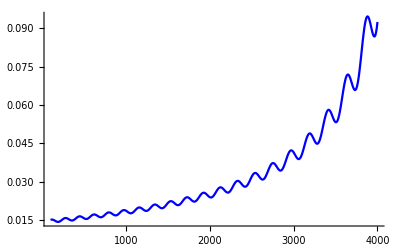

```mathematica
Plot[Abs[sgmoins[0,q]^2*att/(lambda*q*p*be[q])],{q,100,4000},AxesOrigin->{0,0},PlotRange->All,PlotStyle->{RGBColor[0,0,1]}]
```